```mathematica
1/(3360 b^2(-3+a-10 b+6 a b))(-784 b+352 (-1+√(1+b))+b √(1+b) (923+4 b (-30+11 b))+a (-96 (-1+√(1+b))+b (336-393 √(1+b)+4 b √(1+b) (68+11 b))))==1/(3360 b √b)105   ArcSinh[√b]
```

```mathematica
tabb=Table[{a,b /.NSolve[1/(3360 b^2(3-a+10 b-6 a b))(-784 b+352 (-1+√(1+b))+b √(1+b) (923+4 b (-30+11 b))+a (-96 (-1+√(1+b))+b (336-393 √(1+b)+4 b √(1+b) (68+11 b))))==1/(3360 b √b)105   ArcSinh[√b] ,b,PositiveReals ][[1]]},{a,0.2,0.9,0.05}]
```

{{0.2,4.45197},{0.25,4.05343},{0.3,3.68035},{0.35,3.32985},{0.4,2.99946},{0.45,2.687},{0.5,2.39056},{0.55,2.10846},{0.6,1.83919},{0.65,1.58137},{0.7,1.33375},{0.75,1.09518},{0.8,0.864547},{0.85,0.640797},{0.9,0.422868}}

```mathematica
f=Interpolation[tabb]
```

InterpolatingFunction[…]

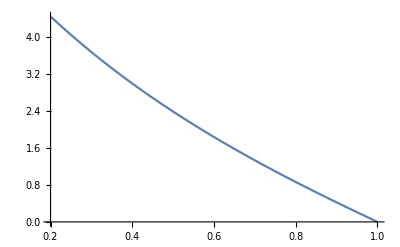

```mathematica
Plot[f[a],{a,0.2,1.0}]
```

```mathematica
√(1+b)(9+4 (-2+b) b+a (-3+4 b (4+b)))/(3-a+10 b-6 a b) == 3 ArcSinh[√b]/ √b
```

```mathematica
tabb1=Table[{a,b/.NSolve[√(1+b)(9+4 (-2+b) b+a (-3+4 b (4+b)))/(9-3a+30 b-18 a b) ==  ArcSinh[√b]/ √b ,b,Reals][[1]]},{a,0.2,0.9,0.05}]
```

{{0.2,12.4251},{0.25,11.1787},{0.3,10.0442},{0.35,9.00872},{0.4,8.06102},{0.45,7.1916},{0.5,6.3923},{0.55,5.65604},{0.6,4.97669},{0.65,4.34893},{0.7,3.76808},{0.75,3.23007},{0.8,2.7313},{0.85,2.26865},{0.9,1.83933}}

```mathematica
g=Interpolation[tabb1]
```

InterpolatingFunction[…]

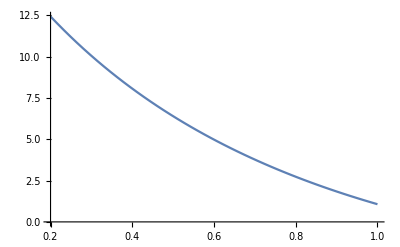

```mathematica
Plot[g[a],{a,0.2,1.0}]
```

```mathematica
.08.08.08.08.08
```

```mathematica
.08.08.08.08.08
```

```mathematica
Sqrt[b+1] (4 (1+a)b^2  + (16a-8)b + (9-3a))/((30-18a)b + (9-3a))
```

(√(1+b) (9-3 a+(-8+16 a) b+4 (1+a) b^2))/(9-3 a+(30-18 a) b)

```mathematica
tabb1=Table[{a,b/.NSolve[√(1+b)(9+4 (-2+b) b+a (-3+4 b (4+b)))/(9-3a+30 b-18 a b) ==  ArcSinh[√b]/ √b ,b,Reals][[1]]},{a,0.2,0.9,0.05}]
```